# Iterated Function Projects

## Meraf Haileslassie

Let us define ColVar(n) = 3n+5 is n if odd, and ColVar(n) = n/2 if n is even.  We will find cycles that could be observed in the trajectories for positive integers n? How often does each cycle occur? Are the proportion stable as n increases? We will look at the height and stopping time of the trajectories. Compare with the original collatz function we looked at in class.  And we will also investigate two additional questions.

## The Collatz function

```mathematica
colVar[n_?OddQ]:=3n+5
colVar[n_?EvenQ]:= n/2
```

```mathematica
colVar/@Range[30]
```

{8,1,14,2,20,3,26,4,32,5,38,6,44,7,50,8,56,9,62,10,68,11,74,12,80,13,86,14,92,15}

## What cycles do we observe

We will use a function that takes three inputs: a function, a starting value and a number of iterations; it returns a sequence of iterates.

```mathematica
findCycle[func_,start_,maxIter_:10000]:=Module[
{seq={start} (* a list to store the sequence that we compute *),
n=start (* the current value *),
p  (* position of a repeated value, if we find a repeated value *)
},

(* main loop: repeat until we find a repeated value or maxIter iterations*)
Do[
(* compute the next iterate *)
n=func[n];
If[MemberQ[seq,n],p=Position[seq,n][[1,1]];Return[seq[[p;;]],Module]];

(* check if we have seen this value before, if so, return the cycle *)
 AppendTo[seq,n]


(* otherwise, append the value to the sequence *)


,maxIter];

(* if we get here, then we didn't find a repeated value *)
False
]
```

```mathematica
findCycle[colVar,74]
```

{74,37,116,58,29,92,46,23}

```mathematica
findCycle[colVar,23]
```

{23,74,37,116,58,29,92,46}

```mathematica
findCycle[colVar,60]
```

{20,10,5}

```mathematica
findCycle[colVar,70]
```

{20,10,5}

```mathematica
findCycle[colVar,38]
```

{38,19,62,31,98,49,152,76}

```mathematica
findCycle[colVar,1000]
```

{20,10,5}

```mathematica
Tally[Table[findCycle[colVar,n],{n,1,500}]]
```

{{{1,8,4,2},1},{{2,1,8,4},1},{{38,19,62,31,98,49,152,76},239},{{4,2,1,8},1},{{5,20,10},1},{{8,4,2,1},64},{{10,5,20},1},{{20,10,5},98},{{19,62,31,98,49,152,76,38},1},{{23,74,37,116,58,29,92,46},1},{{29,92,46,23,74,37,116,58},1},{{31,98,49,152,76,38,19,62},1},{{37,116,58,29,92,46,23,74},1},{{46,23,74,37,116,58,29,92},1},{{49,152,76,38,19,62,31,98},1},{{92,46,23,74,37,116,58,29},24},{{58,29,92,46,23,74,37,116},1},{{62,31,98,49,152,76,38,19},9},{{74,37,116,58,29,92,46,23},14},{{76,38,19,62,31,98,49,152},1},{{98,49,152,76,38,19,62,31},5},{{116,58,29,92,46,23,74,37},6},{{374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748},4},{{152,76,38,19,62,31,98,49},4},{{1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814,407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668},5},{{187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748,374},1},{{3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748,374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091},3},{{283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748,374,187,566},1},{{1496,748,374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992},3},{{347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814,407,1226,613,1844,922,461,1388,694},1},{{359,1082,541,1628,814,407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718},1},{{407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814},1},{{427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748,374,187,566,283,854},1},{{461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814,407,1226,613,1844,922},1},{{1436,718,359,1082,541,1628,814,407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872},1}}

We can see different cycles for different starting values the most common ones i.e. .These cycles are 
1.  {20,10,5},
2.  {8,4,2,1},
3.  {38,19,62,31,98,49,152,76},
4.  {23,74,37,116,58,29,92,46},
5. {374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748}, and 
6. {407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668,1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814}.

## How often do each cycles occur?

```mathematica
check0=Table[Min[findCycle[colVar,n]],{n,1,100}];
TableForm[Tally[check0]]
```

1 | 15
19 | 54
5 | 20
23 | 11

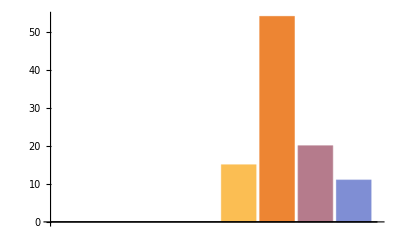

```mathematica
data0 = {{"1",15},{"19",54},{"5",20},{"23",11}};
transposedData0=Transpose[data0]//BarChart
```

Looking at a small range of 100 omits the cycles that we discovered in the pervious question. So let us increase the range to a 1000.

```mathematica
check1=Table[Min[findCycle[colVar,n]],{n,1,1000}];
TableForm[Tally[check1]]
```

1 | 142
19 | 494
5 | 200
23 | 96
187 | 36
347 | 32

We can begin by setting the starting values range from 1 to 1000, it shows that  out of 1000 494 have a cycle that starts with 19. While 32 (the lowest number of trajectories) start with 347.

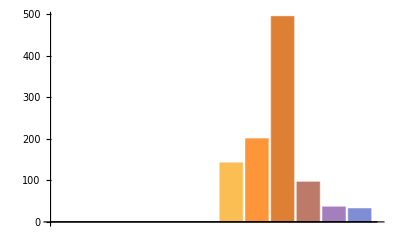

```mathematica
data1 = {
{"1",142},
{"5",200},
{"19",494},
{"23",96},
{"187",36},
{"347",32}};
TransposedData1 = Transpose[data1]//BarChart
```

We have a high percentage of trajectories that contain the cycle that starts with 19. Let us look at  for 10,000.

```mathematica
check2=Table[Min[findCycle[colVar,n]],{n,1,10000}];
TableForm[Tally[check2]]
```

1 | 1436
19 | 4817
5 | 2000
23 | 953
187 | 371
347 | 423

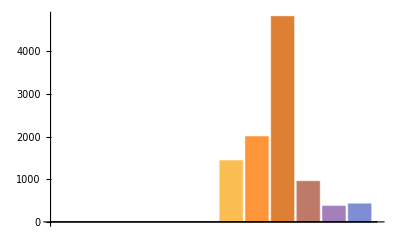

```mathematica
data2= {
{"1",1436},
{"5",2000},
{"19",4817},
{"23",953},
{"187",371},
{"347",423}};
TransposedData2 = Transpose[data2]//BarChart
```

We again see that high percentage of trajectories that contain the cycle start with 19. One thing interesting we can see here is that 347 seems to have an unstable rise in trajectories. Let us investigate more.

```mathematica
ratios[numstarts_]:=Module[
{list,app},
list=Tally[Table[Sort[findCycle[colVar,n]],{n,1,numstarts}]];
app = Table[list[[n,2]],{n,1,6}];
Table[N[app[[{n,2}]]/numstarts][[1]],{n,1,6}]
]
```

```mathematica
table=TableForm[Table[ratios[x],{x,1000,51001,10000}],
TableHeadings->{{10000,50000,70000,80000,90000,100000},{1,19,5,23,187,347}}]
```

| 1 | 19 | 5 | 23 | 187 | 347
10000 | 0.142 | 0.494 | 0.2 | 0.096 | 0.036 | 0.032
50000 | 0.143091 | 0.484909 | 0.2 | 0.0941818 | 0.0364545 | 0.0413636
70000 | 0.14181 | 0.489952 | 0.2 | 0.0930952 | 0.0340476 | 0.0410952
80000 | 0.141581 | 0.493871 | 0.2 | 0.0919355 | 0.033 | 0.0396129
90000 | 0.142463 | 0.494463 | 0.2 | 0.0915122 | 0.0328049 | 0.0387561
100000 | 0.141647 | 0.495255 | 0.2 | 0.0916667 | 0.0328431 | 0.0385882

This computation helps us understand the consistency of the ratio’s more.  We can  draw a conclusion that the ratio for the starting value 1 decreases, for 19 it increases, 5 stays the same,23 decreases, 187 ratio decreases, 347 decreases. The longer cycles seem less stable relative to the shorter cycles.

## Heights of the trajectories and stopping times

We will write a module that computes the sequence of the Collatz iterates from a starting integer n. This module will include a maxiter parameter with a default value of 100,000. So that if the length of the trajectory reaches maxiter, the break statement ends the loop so that it doesn’t run for a long time.

```mathematica
computeTrajectory[start_,maxIter_:100000]:=Module[
{n=start,traj={start}},
(* compute the trajectory until we find 1 *)
While[!MemberQ[traj[[1;;-2]],n],(*In my while loop as *)
n=colVar[n];
AppendTo[traj,n];
If[Length[traj]==maxIter,Break[]] (* quit if the length of the trajectory reaches maxIter *)
];
(* return the trajectory *)
traj
]
```

```mathematica
height[n_]:=Max[computeTrajectory[n]](*testing out the to see if i get a height*)
```

```mathematica
SortBy[Tally[height/@Range[10000]],Last]
```

We can see that the most common height is 46,160.

```mathematica
plottraj[trajectory_]:=ListPlot[trajectory, PlotRange->All,AxesLabel->{"iteration","value"},Joined->True, PlotStyle->Orange,Mesh->All,MeshStyle->{Blue, PointSize[Medium]}]
```

{135,410,205,620,310,155,470,235,710,355,1070,535,1610,805,2420,1210,605,1820,910,455,1370,685,2060,1030,515,1550,775,2330,1165,3500,1750,875,2630,1315,3950,1975,5930,2965,8900,4450,2225,6680,3340,1670,835,2510,1255,3770,1885,5660,2830,1415,4250,2125,6380,3190,1595,4790,2395,7190,3595,10790,5395,16190,8095,24290,12145,36440,18220,9110,4555,13670,6835,20510,10255,30770,15385,46160,23080,11540,5770,2885,8660,4330,2165,6500,3250,1625,4880,2440,1220,610,305,920,460,230,115,350,175,530,265,800,400,200,100,50,25,80,40,20,10,5,20}

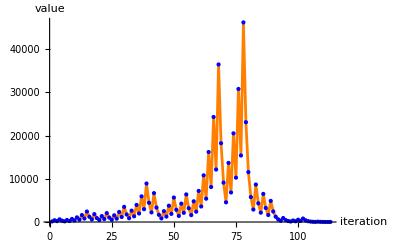

```mathematica
traj=computeTrajectory[135]
plottraj[traj]
```

```mathematica
Length[computeTrajectory[135]]
```

113

From the plot below are see that there are lines pointing outwards from the origin and some lines running parallel to the x axis at different heights. The straight horizontal line that appear at the height of  46,160. From the computation above we can see that the starting integer for this height is 135. There seems to be a large concentration of heights around the origin.

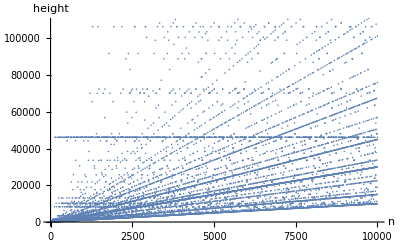

```mathematica
heightList=height/@Range[10000];
ListPlot[heightList,AxesLabel->{"n","height"}]
```

### Let us look at the stopping time.

```mathematica
stop[startList_,maxIter_:100000]:=Module[{n,traj,stopList},(*iterate over the list of starting values*)stopList=Table[n=start;
traj={start};
(*compute the trajectory until we find 1 or a repeated value*)While[!MemberQ[traj[[1;;-2]],n],n=colVar[n];
AppendTo[traj,n];
If[Length[traj]==maxIter,Break[]]];
(*append the length of the trajectory to the list*)Length[traj],{start,startList}];
(*return the list of stopping times*)stopList]
```

Let us look at the most common stopping time.

```mathematica
ReverseSortBy[Tally[stop[Range[1,1000]]],Last]
```

{{45,43},{17,29},{27,27},{14,27},{35,26},{30,25},{25,25},{32,24},{24,23},{19,23},{37,22},{22,22},{9,22},{40,21},{29,21},{28,21},{20,21},{12,20},{16,19},{34,18},{21,18},{15,18},{23,17},{18,17},{13,16},{47,15},{33,15},{26,15},{11,15},{53,14},{48,14},{42,14},{31,14},{46,13},{38,13},{36,13},{10,13},{50,12},{43,11},{58,10},{52,9},{44,9},{39,9},{66,8},{49,8},{74,7},{71,7},{60,7},{56,7},{55,7},{41,7},{84,5},{61,5},{57,5},{51,5},{5,5},{121,4},{113,4},{110,4},{108,4},{87,4},{81,4},{79,4},{76,4},{69,4},{65,4},{63,4},{54,4},{8,4},{118,3},{115,3},{105,3},{100,3},{97,3},{78,3},{68,3},{7,3},{4,3},{114,2},{112,2},{109,2},{107,2},{95,2},{92,2},{77,2},{75,2},{73,2},{70,2},{67,2},{62,2},{59,2},{6,2},{126,1},{123,1},{120,1},{117,1},{111,1},{106,1},{104,1},{102,1},{99,1},{94,1},{89,1},{86,1},{83,1},{82,1},{80,1},{72,1},{64,1}}

We can see that the most popular stopping time is 45, for 1000 values. This can help us understand the concentration of stopping times in our graph below.

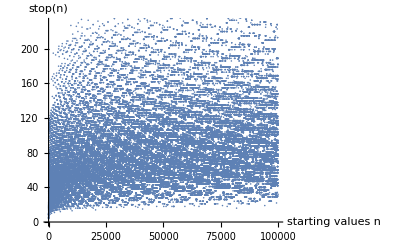

```mathematica
stoplist=Range[1,100001];
stoptime=stop[stoplist];
ListPlot[stoptime,AxesLabel->{"starting values n","stop(n)"}]
```

We can see short horizontal lines to illustrate the the same stopping times for different values of n which shows less overlapping and regularity. The pseudo-strings of similar stopping times as seen by the horizontal clumps of values. It appears there is a concentration around 35 to 40.

## Compare col_5 and col

We observed different cycles present in this function double the amount than the original collatz function. We can see different patterns when we compare the different variant of the function. We distinguish several cycles in this function. We can see that certain cycles appear more frequently than others i.e those starting with 38,20,8. When we looked at the height of the trajectories we can see that the most common height (46,160) is much larger than the height of the collatz function we looked at in class (9,232), when we divide these two numbers we get 5 which is something that we see again in further investigation (starting values for the most common height) . There is also less variety in stopping times than in the original collatz function. The new most common stopping time is 45 which is greater than the collatz function we looked at in class (29). The new function has more stopping times that finish at the same time (we see less overlapping relative to the collatz function we looked at in class). We can further visualize this by looking at the graph. Here we don’t have an overlap, this would imply some regularity in the new function.

## Further investigation

## Why one fifth of first 10,000 have the five loop?

After further consideration, I believe that a multiple of 5 will never not become a multiple of 5 due to the col_5 function. For example,

```mathematica
computeTrajectory[150]
```

{150,75,230,115,350,175,530,265,800,400,200,100,50,25,80,40,20,10,5,20}

Throughout the trajectory the values are a multiple of 5. This makes sense because of the function we are studying. When the value is a multiple of 5, dividing by two would transform it into another multiple, either odd or even. If it’s an odd multiple of 5, multiplying by three and adding 5 keeps it a multiple. In the initial 200,000 values, all multiples of 5 seem to reach a cycle of 5. Beyond that, I haven’t checked, but I anticipate the pattern continues.

## What happens when we input negative values?

```mathematica
Table[{computeTrajectory[n],n},{n,-1,-30,-1}]
```

{{{-1,2,1,8,4,2},-1},{{-2,-1,2,1,8,4,2},-2},{{-3,-4,-2,-1,2,1,8,4,2},-3},{{-4,-2,-1,2,1,8,4,2},-4},{{-5,-10,-5},-5},{{-6,-3,-4,-2,-1,2,1,8,4,2},-6},{{-7,-16,-8,-4,-2,-1,2,1,8,4,2},-7},{{-8,-4,-2,-1,2,1,8,4,2},-8},{{-9,-22,-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-9},{{-10,-5,-10},-10},{{-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-11},{{-12,-6,-3,-4,-2,-1,2,1,8,4,2},-12},{{-13,-34,-17,-46,-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-13},{{-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-14},{{-15,-40,-20,-10,-5,-10},-15},{{-16,-8,-4,-2,-1,2,1,8,4,2},-16},{{-17,-46,-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-17},{{-18,-9,-22,-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-18},{{-19,-52,-26,-13,-34,-17,-46,-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-19},{{-20,-10,-5,-10},-20},{{-21,-58,-29,-82,-41,-118,-59,-172,-86,-43,-124,-62,-31,-88,-44,-22,-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-21},{{-22,-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-22},{{-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-23},{{-24,-12,-6,-3,-4,-2,-1,2,1,8,4,2},-24},{{-25,-70,-35,-100,-50,-25},-25},{{-26,-13,-34,-17,-46,-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-26},{{-27,-76,-38,-19,-52,-26,-13,-34,-17,-46,-23,-64,-32,-16,-8,-4,-2,-1,2,1,8,4,2},-27},{{-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-28},{{-29,-82,-41,-118,-59,-172,-86,-43,-124,-62,-31,-88,-44,-22,-11,-28,-14,-7,-16,-8,-4,-2,-1,2,1,8,4,2},-29},{{-30,-15,-40,-20,-10,-5,-10},-30}}

Something interesting we can see is that the trajectories either get to positive 1 or get stuck in a cycle between -5 and -10. Let us look at the cycles with negative starting values.

```mathematica
Tally[Table[Sort[findCycle[colVar,n]],{n,-1,-100000,-1}]]
```

{{{1,2,4,8},80000},{{-10,-5},6502},{{-100,-70,-50,-35,-25},6451},{{-1360,-910,-820,-680,-610,-550,-455,-410,-370,-340,-305,-275,-250,-205,-185,-170,-125,-85},7047}}

We have 4 cycles in the first 100,000 negative starting values: 
 		{1,2,4,8}
 		{-10,-5}
 		{-100,-70,-50,-35,-25}
{-1360,-910,-820,-680,-610,-550,-455,-410,-370,-340,-305,-275,-250,-205,-185,-170,-125,-85}

```mathematica
colneg[n_?OddQ]:=3n-5
colneg[n_?EvenQ]:=n/2
```

```mathematica
Tally[Table[ReverseSort[findCycle[colneg,n]],{n,1,100000}]]
```

{{{-1,-2,-4,-8},80000},{{10,5},6502},{{100,70,50,35,25},6451},{{1360,910,820,680,610,550,455,410,370,340,305,275,250,205,185,170,125,85},7047}}

When comparing it too the collatz variant the cycles have the same values but are opposite sign.